```mathematica
Mixing (one scat, one bound)
```

## DEFINE PARAMTERS

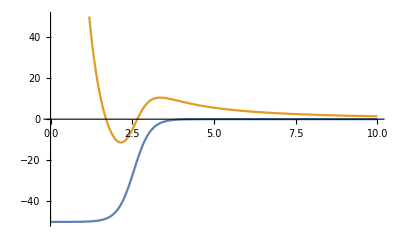

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=50;R=2.55;a=0.25;μ=8/9 Subscript[m, N];
E2=3;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## SOLUTIONS

```mathematica
(*DEFINITIONS*)
```

```mathematica
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wave0[En_,r_,δ_]:=Cos[δ]SphericalBesselJ[0,k0[En] r]-Sin[δ] SphericalBesselY[0,k0[En] r];
wave2[En_,r_]:=SphericalHankelH1[2,k2[En] r];
B0[En_,δ_]:=rmax/wave0[En,rmax,δ](D[wave0[En,r,δ],r]/.r->rmax);
B2[En_]:=rmax/wave2[En,rmax](D[wave2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnew[En_,δ_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B0[En,δ]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B2[En]/rmax-1);H];
(*RETURNS PARAMETERS*)
eigenv[En_?NumericQ,i_,δ_?NumericQ]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];eval[[i]]);
findnd[En_?NumericQ]:=Module[{n=3},While[Max[Table[eigenv[En,n,x],{x,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenv[En,n,x]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
```

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
const0[i_]:=evec[[i,-len-1]]/wave0[eval[[i]],rmax,δ];
const2[i_]:=evec[[i,-1]]/wave2[eval[[i]],rmax];
rmaxx=20.;
```

```mathematica
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];Print[{En,eval[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,Part[evec[[n]],1;;len]}],Transpose[{rlist,Part[evec[[n]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], const0[n] wave0[eval[[n]],Range[rmax,rmaxx,dr],δ]}],Transpose[{Range[rmax,rmaxx,dr], const2[n] wave2[eval[[n]],Range[rmax,rmaxx,dr]]}]}]]
```

```mathematica
vals[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];Print[{En,eval[[n]],n,δ}];]
```

{1.,1.+0. ⅈ,3,1.75524+0. ⅈ}

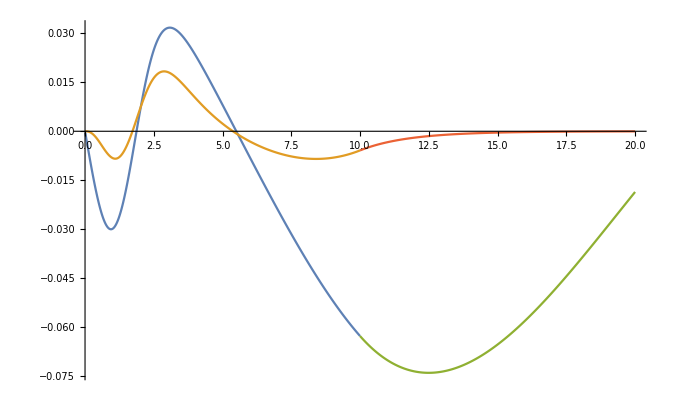
{1132.96,-Graphics-}

```mathematica
wvplot[1.]//Timing(*V0~50MeV*)
```

```mathematica
wvplot[0.1]//Timing(*V0=8MeV*)
```

$Aborted